```mathematica
gcp = Compile[{{x}, {y}, {z}},16/N[Pi]^2*Sum[1/(n*m)*Exp[-N[Pi]*Sqrt[n^2+m^2]*x]*Sin[n*N[Pi]*y]*Sin[m*N[Pi]*z],{n, 1, 20,  2}, {m, 1,20, 2}]]
```

CompiledFunction[…]

```mathematica
Manipulate[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1},PlotRange -> {0, 1},PlotRangeClipping -> False,ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &),  WorkingPrecision->2, PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{x, 0, 0.5, 0.05}]
```

```mathematica
Animate[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1},PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &),  WorkingPrecision->2, PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{x, 0, 0.2, 0.01}, AnimationRate->0.002]
```

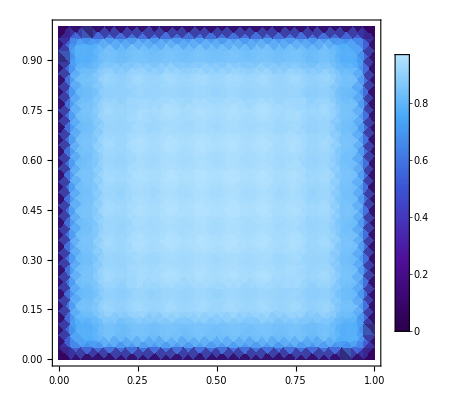
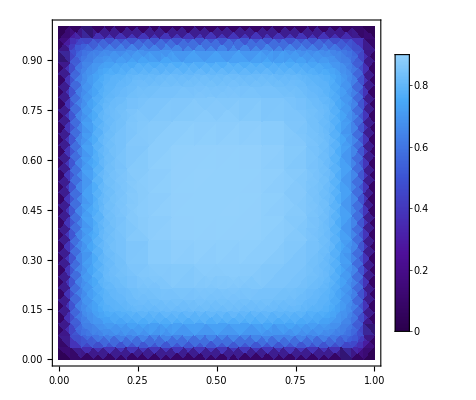
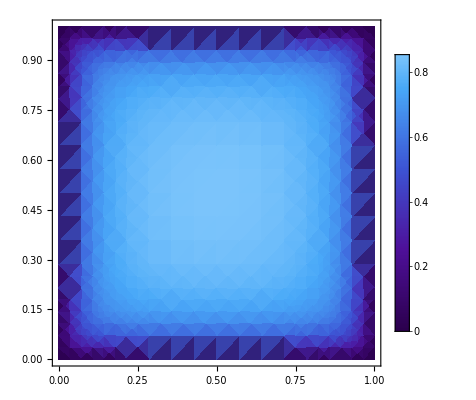
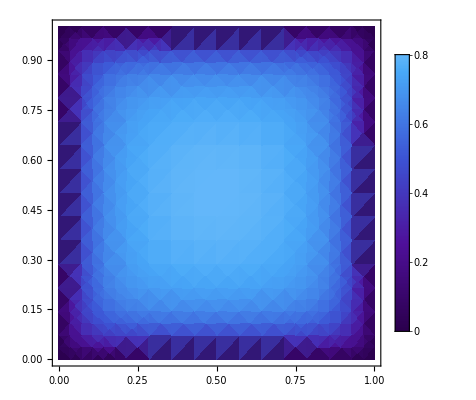
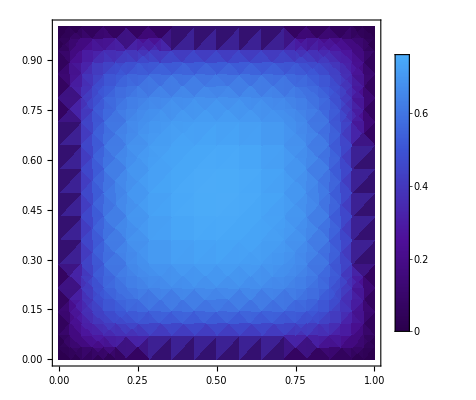
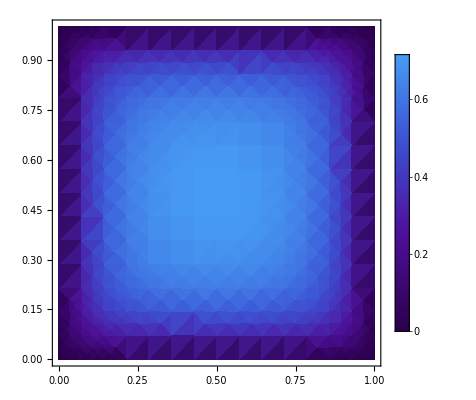
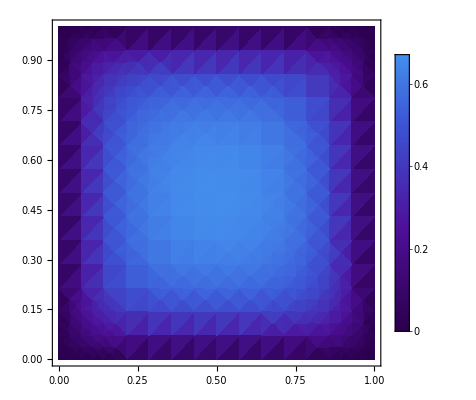
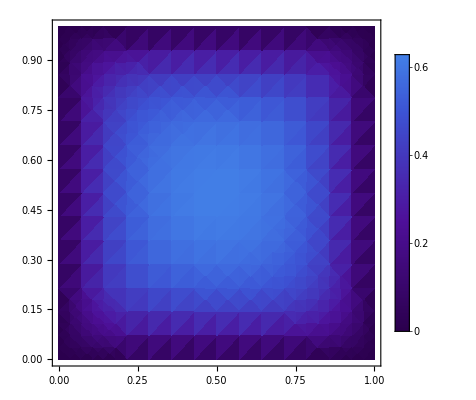

```mathematica
frames = Table[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1}, WorkingPrecision->20, PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{x, 0.02, 0.4, 0.02}]
```

```mathematica
ListAnimate[frames]
```

```mathematica
frames3d1 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{a, 0.02, 0.1, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d2 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{a, 0.12, 0.2, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d3 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{a, 0.22, 0.3, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d4 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{a, 0.32, 0.4, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d = Join[frames3d1, frames3d2, frames3d3,frames3d4]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Rule::argr: "Rule" called with 1 argument; "2" arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

```mathematica
ListAnimate[frames3d, 5]
```